```mathematica
SetDirectory[NotebookDirectory[]];
Get["MyLabData.m"];
```

```mathematica
MLD
```

Hello! It's a small library, consisting of several functions for working with data using Wolfram during laboratory works. 
Original (raw) data may be stored in Excel, and then, using MLDReadExcel[], be stored in Wolfram list of lists. Then, MLDMakeLabData[] or MLDMakeLabDataWOUnits[] transforms it into Wolfram dataset. All other functions are made to work with datasets and only them.

```mathematica
rawdata=MLDReadExcel["C:\\Users\\mrgeb\\OneDrive\\Documents\\вольфрам стафф\\sample_data.xlsx","C 2", "H 12"]
```

{{x,dx,t,dt,a,da},{m,m,s,s,,},{1.,0.01,1.05,0.05,15.,1.},{1.2,0.01,1.47,0.05,19.,1.},{1.4,0.01,2.01,0.05,25.,1.},{1.6,0.02,2.5,0.05,31.,1.},{1.8,0.02,3.24,0.05,36.,1.},{2.,0.02,3.98,0.05,42.,1.},{2.2,0.03,4.79,0.05,45.,1.},{2.4,0.03,5.7,0.05,51.,1.},{2.6,0.03,6.68,0.05,55.,1.}}

```mathematica
data=MLDMakeLabData[rawdata]
```

```mathematica
?MLDMakeLabData
```

```mathematica
data=MLDMakeColumnWErrors[data,"x±","x","dx"];
data=MLDMakeColumnWErrors[data,"t±","t","dt"];
data=MLDMakeColumnWErrors[data,"a±",5,6]
```

```mathematica
?MLDMakeColumnWErrors
```

```mathematica
p=Quantity[4.3,"kg"];
data=data[All, Append[#, "V" -> #["t±"]*#["a±"]*p]&]
```

```mathematica
data=data[All,{"x", "x±","V"}];
data //MLDRenameColumn[#,"x","x0"]&//MLDRenameColumn[#,2,"x"]&
data=data[All,<|"x0"->1,"x"->2, "V"->3|>]
```

```mathematica
MLDFindColumnWithName[data,"x"]
```

2

```mathematica
fit=MLDNonLinearFit[data,"x0","V",α x^3+β x^2 + γ x +δ, {α,β,γ,δ},x,Weights->Automatic]
```

FittedModel[…]

```mathematica
fit["ParameterTable"]
fit["AdjustedRSquared"]
```

| Estimate | Standard Error | t-Statistic | P-Value
α | 43.1521 | 31.7722 | 1.35817 | 0.232479
β | 269.975 | 159.888 | 1.68853 | 0.152109
γ | -474.776 | 255.355 | -1.85928 | 0.122084
δ | 228.907 | 129.233 | 1.77127 | 0.136724

0.999628

```mathematica
MLDFitForm[fit][t]//Simplify
```

t (-475.255.)+t^3 (43.32.)+(229.129.)+t^2 (270.160.)

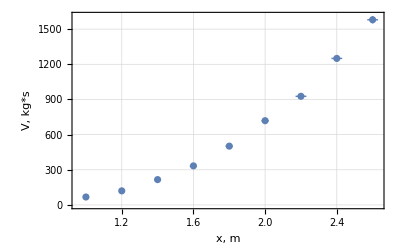

```mathematica
dotsplot=ListPlot[data[All,{"x","V"}], PlotTheme->"Detailed", FrameLabel->{"x, m","V, kg*s"}]
```

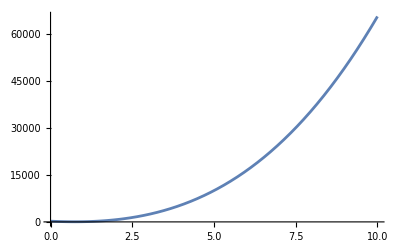

```mathematica
fitplot=Plot[fit[x],{x,0,10}]
```

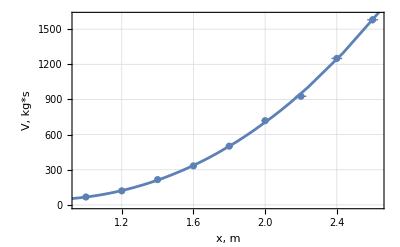

```mathematica
Show[dotsplot,fitplot]
```

```mathematica
data[[Values]]//Normal
```

{{1. m,(1.0000.010) m,(68.6.) kg s},{1.2 m,(1.2000.010) m,(120.8.) kg s},{1.4 m,(1.4000.010) m,(216.10.) kg s},{1.6 m,(1.6000.020) m,(333.13.) kg s},{1.8 m,(1.8000.020) m,(502.16.) kg s},{2. m,(2.0000.020) m,(719.19.) kg s},{2.2 m,(2.2000.030) m,(927.23.) kg s},{2.4 m,(2.4000.030) m,(1250.27.) kg s},{2.6 m,(2.6000.030) m,(1580.31.) kg s}}

```mathematica
MLDTexTableWErrors[data[[Values]]//Normal]
```

\begin{table}
  \centering 
  \begin{tabular}{|c|c|c|} 
     \hline 
     %insert columns' names manually into the line below!!! 
     \\ \hline 
     $1.$ & $1. \pm 0.01$ & $67.725 \pm 5.5485$ \\ 
     $1.2$ & $1.2 \pm 0.01$ & $120.099 \pm 7.52611$ \\ 
     $1.4$ & $1.4 \pm 0.01$ & $216.075 \pm 10.178$ \\ 
     $1.6$ & $1.6 \pm 0.02$ & $333.25 \pm 12.6485$ \\ 
     $1.8$ & $1.8 \pm 0.02$ & $501.552 \pm 15.9376$ \\ 
     $2.$ & $2. \pm 0.02$ & $718.788 \pm 19.3502$ \\ 
     $2.2$ & $2.2 \pm 0.03$ & $926.865 \pm 22.7561$ \\ 
     $2.4$ & $2.4 \pm 0.03$ & $1250.01 \pm 26.8509$ \\ 
     $2.6$ & $2.6 \pm 0.03$ & $1579.82 \pm 31.0628$ \\ 
     \hline 
   \end{tabular} 
 \end{table}

```mathematica
?MLDTexTableWErrors
```

```mathematica
MLDHelp
```

MLDReadExcel[path_, topleft_, bottomright_] (*cells of format "AB 12" *)
MLDMakeLabDataWOUnits[rawdata_]
MLDMakeLabData[rawdata_] (*from a list of lists, where 1st row is names of columns*)

MLDMakeColumnWErrors[data_,name_,values_,errs_] (*values_ end errs_ are names or indeces*)
MLDSetUnit[data_, column_, unit_]
MLDConvertUnit[data_, column_, unit_](*column_ is name or index*)

MLDFindColumnWithName[data_,name_]
MLDRenameColumn[data_, old_, name_] (*old_ is name or index*)

MLDNonLinearFit[data_,xcol_,ycol_,form_,params_,x_,options_]
MLDLinearFit[data_,xcol_,ycol_,funcs_,x_,options_] (*options_ are of format { , , }!!!*)